### Basic:

```mathematica
FNJ=FileNameJoin;
```

```mathematica
RelativeDir[dir_]:=FileNameJoin[{NotebookDirectory[],dir}]
```

```mathematica
Replicate[list_,n_]:=Flatten[Transpose[ConstantArray[list,n]]]
```

```mathematica
ToText[list_]:=StringJoin[Riffle[ToString[#]&/@list,"\n"]]
```

```mathematica
ShiftLeft[list_,n_]:=Drop[PadLeft[list,Length[list]+n],-n]
```

```mathematica
ShiftRight[list_,n_]:=Drop[PadRight[list,Length[list]+n],n]
```

### Before simulation:

```mathematica
(*-------parameters-------*)
td = 3; blocks = 4; l = 100;
(*------------------------*)
data=RandomInteger[{-16,16},l];
ker = RandomInteger[{-16,16},td*blocks];
upKer = RandomInteger[{-16,16},td*6];
```

```mathematica
expected=ListConvolve[Reverse[ker],data,1,0];
```

```mathematica
Max[Abs[expected]]
```

727

```mathematica
Export[RelativeDir["data.dat"],ToText[Replicate[data,td]]];Export[RelativeDir["coefs.dat"],ToText[ker]];Export[RelativeDir["upsamp_coefs.dat"],ToText[upKer]];
```

### After simulation:

```mathematica
ker
```

{-2,-13,-9,12,-4,-12,1,-5,7,-16,7,-7}

```mathematica
expected
```

{105,7,30,207,-135,46,223,415,-468,115,458,467,-457,18,227,22,80,120,-95,128,113,258,-337,166,-11,96,9,74,328,-432,320,186,-71,-346,350,-198,-105,-110,406,-133,-103,162,-247,-12,332,88,-456,-460,304,-19,29,-552,-89,28,68,-392,-220,82,-8,-426,-313,727,-623,10,-60,210,-495,140,-3,-508,205,123,-322,-518,320,269,-471,341,308,149,-323,506,168,97,-151,486,142,87,-59,265,-190,-330,0,-147,-295,249,-271,-242,-153,-202}

```mathematica
upKer
```

{-10,-15,-13,-7,-5,-15,-12,-10,7,8,6,-9,16,-14,-16,15,-14,8}

```mathematica
Max[lol]
```

1849

```mathematica
upIn=Flatten@Riffle[expected,{ConstantArray[0,2]}]
```

{105,0,0,7,0,0,30,0,0,207,0,0,-135,0,0,46,0,0,223,0,0,415,0,0,-468,0,0,115,0,0,458,0,0,467,0,0,-457,0,0,18,0,0,227,0,0,22,0,0,80,0,0,120,0,0,-95,0,0,128,0,0,113,0,0,258,0,0,-337,0,0,166,0,0,-11,0,0,96,0,0,9,0,0,74,0,0,328,0,0,-432,0,0,320,0,0,186,0,0,-71,0,0,-346,0,0,350,0,0,-198,0,0,-105,0,0,-110,0,0,406,0,0,-133,0,0,-103,0,0,162,0,0,-247,0,0,-12,0,0,332,0,0,88,0,0,-456,0,0,-460,0,0,304,0,0,-19,0,0,29,0,0,-552,0,0,-89,0,0,28,0,0,68,0,0,-392,0,0,-220,0,0,82,0,0,-8,0,0,-426,0,0,-313,0,0,727,0,0,-623,0,0,10,0,0,-60,0,0,210,0,0,-495,0,0,140,0,0,-3,0,0,-508,0,0,205,0,0,123,0,0,-322,0,0,-518,0,0,320,0,0,269,0,0,-471,0,0,341,0,0,308,0,0,149,0,0,-323,0,0,506,0,0,168,0,0,97,0,0,-151,0,0,486,0,0,142,0,0,87,0,0,-59,0,0,265,0,0,-190,0,0,-330,0,0,0,0,0,-147,0,0,-295,0,0,249,0,0,-271,0,0,-242,0,0,-153,0,0,-202}

```mathematica
lol=ListConvolve[Reverse[upKer],upIn,1,0]
```

{840,-1470,1575,-1624,-1568,1785,-817,112,1402,1848,-4326,2381,-6188,-1423,708,-595,578,-1273,3171,-6901,237,-5102,-8791,10032,-12735,-810,-273,7299,6997,-4091,4998,-16785,-2035,-17027,-13000,15734,-12820,-2427,2027,10818,10813,-4927,545,-14857,-9923,-19776,-8013,1741,-845,-4966,1681,6742,1827,4976,-6885,-1495,-898,-1257,-4057,-2024,-935,-5874,763,-4401,-5276,6202,-7080,-821,-2094,4504,3597,-2140,-1264,-9257,-5372,-8248,191,3700,1498,-5381,-630,1398,3749,4362,38,-8969,3441,-10604,1495,-1310,5655,1311,-1399,1325,-13461,-90,-15330,1880,6619,1150,994,-8934,11093,2538,-1006,-11517,-9224,-3788,-4597,7367,846,11145,1117,-5982,3815,646,6876,-8885,-7692,2767,1029,10335,3610,9998,-3559,-3334,-9232,1522,-2083,-1606,203,-4729,9479,-5072,2919,-7320,-2747,9396,-6529,6069,-2523,8539,13797,-14922,9688,-2912,-9708,-9704,-7610,2435,276,7244,10395,10247,13308,-3836,9146,14718,-7235,3152,-7213,-8675,-3155,3782,7367,2804,7919,74,12607,17421,-3221,8917,95,-5548,-3524,804,3380,-562,9708,-1158,13354,16458,-7099,16232,-5382,4211,-17727,-264,4131,7808,18324,2816,20289,-2353,-7997,-8647,5250,7787,-6816,-4260,-7574,14679,16125,2740,4431,-6838,-3965,-11111,12794,-1478,15470,2149,-5392,6590,-885,5067,-11720,7011,3495,8995,13033,-10812,18136,6205,-3895,-5070,-11824,5964,-11347,9693,7039,22039,7654,2737,5064,-8432,6020,-18297,-5787,10460,-1785,-806,-3482,11039,612,2241,-11855,-19519,678,-14966,-2809,7944,2178,-3916,-4670,3216,-3473,3322,-13700,-19098,1298,-10646,-1785,6918,1264,-5100,-4102,-2052,-3947,131,-13068,-10274,-5980,-5549,6895,-7191,8599,-180,-10437,-2744,1538,-3830,-2913,6463,-4137,15455,4262,2049,-236,4958,2623,299,12361,-1405,13166,5094,-7788,1213}

```mathematica
2^13
```

8192

```mathematica
Floor[lol/2^8]
```

{3,-6,6,-7,-7,6,-4,0,5,7,-17,9,-25,-6,2,-3,2,-5,12,-27,0,-20,-35,39,-50,-4,-2,28,27,-16,19,-66,-8,-67,-51,61,-51,-10,7,42,42,-20,2,-59,-39,-78,-32,6,-4,-20,6,26,7,19,-27,-6,-4,-5,-16,-8,-4,-23,2,-18,-21,24,-28,-4,-9,17,14,-9,-5,-37,-21,-33,0,14,5,-22,-3,5,14,17,0,-36,13,-42,5,-6,22,5,-6,5,-53,-1,-60,7,25,4,3,-35,43,9,-4,-45,-37,-15,-18,28,3,43,4,-24,14,2,26,-35,-31,10,4,40,14,39,-14,-14,-37,5,-9,-7,0,-19,37,-20,11,-29,-11,36,-26,23,-10,33,53,-59,37,-12,-38,-38,-30,9,1,28,40,40,51,-15,35,57,-29,12,-29,-34,-13,14,28,10,30,0,49,68,-13,34,0,-22,-14,3,13,-3,37,-5,52,64,-28,63,-22,16,-70,-2,16,30,71,11,79,-10,-32,-34,20,30,-27,-17,-30,57,62,10,17,-27,-16,-44,49,-6,60,8,-22,25,-4,19,-46,27,13,35,50,-43,70,24,-16,-20,-47,23,-45,37,27,86,29,10,19,-33,23,-72,-23,40,-7,-4,-14,43,2,8,-47,-77,2,-59,-11,31,8,-16,-19,12,-14,12,-54,-75,5,-42,-7,27,4,-20,-17,-9,-16,0,-52,-41,-24,-22,26,-29,33,-1,-41,-11,6,-15,-12,25,-17,60,16,8,-1,19,10,1,48,-6,51,19,-31,4}

```mathematica
result
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,-6,6,-7,-7,6,-4,0,5,7,-17,9,-25,-6,2,-3,2,-5,12,-27,0,-20,-35,39,-50,-4,-2,28,27,-16,19,-66,-8,-67,-51,61,-51,-10,7,42,42,-20,2,-59,-39,-78,-32,6,-4,-20,6,26,7,19,-27,-6,-4,-5,-16,-8,-4,-23,2,-18,-21,24,-28,-4,-9,17,14,-9,-5,-37,-21,-33,0,14,5,-22,-3,5,14,17,0,-36,13,-42,5,-6,22,5,-6,5,-53,-1,-60,7,25,4,3,-35,43,9,-4,-45,-37,-15,-18,28,3,43,4,-24,14,2,26,-35,-31,10,4,40,14,39,-14,-14,-37,5,-9,-7,0,-19,37,-20,11,-29,-11,36,-26,23,-10,33,53,-59,37,-12,-38,-38,-30,9,1,28,40,40,51,-15,35,57,-29,12,-29,-34,-13,14,28,10,30,0,49,68,-13,34,0,-22,-14,3,13,-3,37,-5,52,64,-28,63,-22,16,-70,-2,16,30,71,11,79,-10,-32,-34,20,30,-27,-17,-30,57,62,10,17,-27,-16,-44,49,-6,60,8,-22,25,-4,19,-46,27,13,35,50,-43,70,24,-16,-20,-47,23,-45,37,27,86,29,10,19,-33,23,-72,-23,40,-7,-4,-14,43,2,8,-47,-77,2,-59,-11,31,8,-16,-19,12,-14,12,-54,-75,5,-42,-7,27,4,-20,-17,-9,-16,0,-52,-41,-24,-22,26,-29,33,-1,-41,-11,6,-15,-12,25,-17,60,16,8,-1,19,10,1,48,-6,51,19,-31,4,36,-12,6,21,-24,44,39,-2,24,31,1,19,40,-1,26,52,-27,52,37,-10,20,-8,14,-13,45,26,55,36,-2,36,8,7,-27,-6,15,5,2,10,19,13,7,-6,-3,-4,-8,-8,-6,-2,-2,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
result=Flatten[Import[RelativeDir[FNJ[{"edit_firIP_v1_0.sim","sim_1","behav","xsim","out.dat"}]]]];
```

```mathematica
LongestCommonSubsequence[result,lol]
```

{}

### Random:

```mathematica
2224189. /2^16
```

33.9384

### Samples from fpga:

```mathematica
2^14
```

16384

```mathematica
85*6229+960
```

530425

```mathematica
snaps=Reverse/@Import[RelativeDir["snap10.dat"]];
registers = {"fir_in","sum_loop_out", "sum_loop_end", "count","x","coef_crr","sum_in","sum_out"};
```

```mathematica
firIn=Downsample[snaps[[1]],2,1]; firOut = Downsample[snaps[[2]],2,2];
```

```mathematica
BitShiftRight[firOut,16]
```

{-808,-870,-773,-536,-207,148,459,661,715,609,366,34,-319,-625,-822,-869,-757,-509,-174,179,481,670,708,588,334,-2,-354,-651,-833,-864,-737,-478,-137,214,507,682,705,570,305,-35,-385,-673,-841,-857,-715,-445,-100,248,532,693}

```mathematica
firOutS=Downsample[snaps[[3]],2]
```

{-600,-809,-871,-774,-537,-208,148,459,661,715,609,366,34,-320,-626,-823,-870,-758,-510,-175,179,481,670,708,588,334,-3,-355,-652,-834,-865,-738,-479,-138,214,507,682,705,570,305,-36,-386,-674,-842,-858,-716,-446,-101,248,532}

```mathematica
ker={52,150,393,872,1630,2633,3770,4871,5745,6229,6229,5745,4871,3770,2633,1630,872,393,150,52}
```

{52,150,393,872,1630,2633,3770,4871,5745,6229,6229,5745,4871,3770,2633,1630,872,393,150,52}

```mathematica
ListConvolve[ker,firIn]
```

{14054772,33267127,44745189,46204290,37371889,20031992,-2340782,-25259741,-44131255,-55174024,-56167359,-46891360,-29184679,-6604508,16292402,34880765,45424627,45823061,36013029,17970542,-4690099,-27426384,-45682845,-55802274,-55750681,-45520180,-27146941,-4329981,18318687,36221815,45779846}

```mathematica
firOut
```

{-52957126,-57045866,-50703626,-35175093,-13569241,9758538,30096254,43349108,46869436,39968431,24041994,2279233,-20959773,-41020978,-53889101,-56984195,-49673534,-33403820,-11441120,11783828,31578304,43958256,46453047,38580780,21933273,-151579,-23242434,-42710790,-54654944,-56677116,-48354338,-31333836,-9031638,14054772,33267127,44745189,46204290,37371889,20031992,-2340782,-25259741,-44131255,-55174024,-56167359,-46891360,-29184679,-6604508,16292402,34880765,45424627}

```mathematica
LongestCommonSubsequence[ListConvolve[ker,firIn],firOut]
```

{14054772,33267127,44745189,46204290,37371889,20031992,-2340782,-25259741,-44131255,-55174024,-56167359,-46891360,-29184679,-6604508,16292402,34880765,45424627}

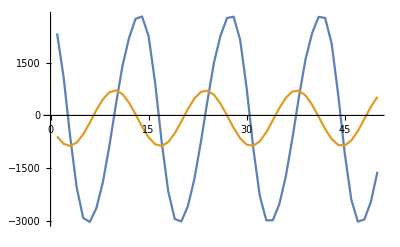

```mathematica
ListPlot[{firIn,firOutS},Joined->True]
```

```mathematica
TableForm[Join[{Range[Length[snaps]]},Transpose@snaps]];
```

```mathematica
rng=Range[#,#+3]&/@Range[1,5*3,3];
```

```mathematica
(*(Drop[ShiftRight[snaps[[#1]],1]+(snaps[[#2]]*snaps[[#3]]),-4]==Drop[snaps[[#4]],4])&@@@rng*)
```

### Upsampling:

```mathematica
upker={0.004349354184333842,-0.012460526975242473,-0.04179305187785534,0.11580155515788863,0.4377645703903624,0.4377645703903624,0.11580155515788867,-0.04179305187785537,-0.012460526975242473,0.004349354184333842};
```

```mathematica
f=0.113;
```

```mathematica
in=Sin[2*π*f*#]&/@Range[100];
```

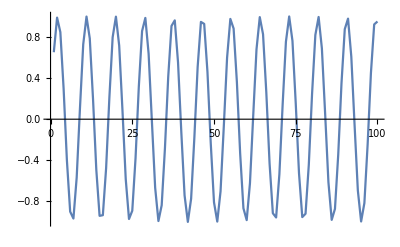

```mathematica
ListPlot[in,Joined->True]
```

```mathematica
inR=Riffle[in,0];
```

```mathematica
out=ListConvolve[upker,inR,1,0];
```

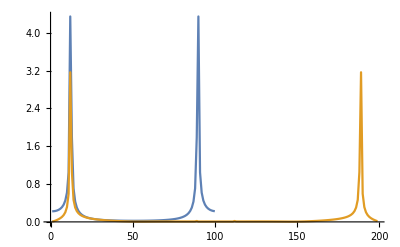

```mathematica
ListPlot[{Abs[Fourier[in]],Abs[Fourier[out]]},Joined->True,PlotRange->All]
```

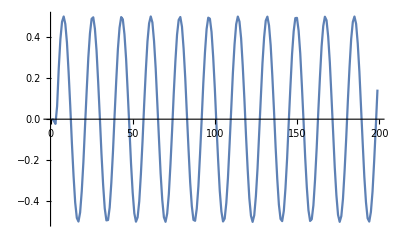

```mathematica
ListPlot[out,Joined->True]
```